```mathematica
config=Import["configweak.dat"];
```

```mathematica
{Min@config,Max@config}
```

{0.018479,0.0831219}

```mathematica
asize=23;
```

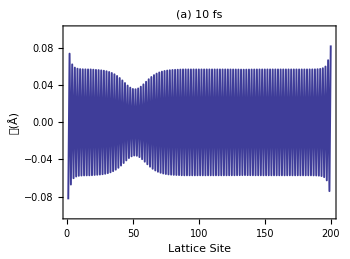

```mathematica
fa[1]=ListPlot[phiToU[config[[1,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(a) 10 fs",Bold,asize]]
```

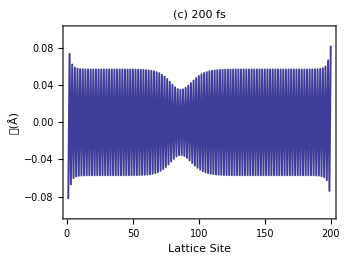

```mathematica
fa[2]=ListPlot[phiToU[config[[20,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(c) 200 fs",Bold,asize]]
```

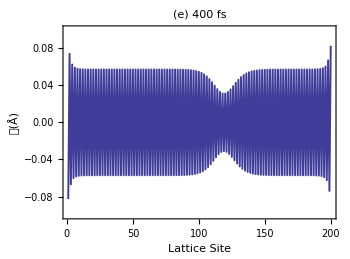

```mathematica
fa[3]=ListPlot[phiToU[config[[40,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(e) 400 fs",Bold,asize]]
```

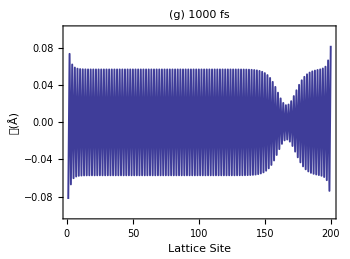

```mathematica
fa[4]=ListPlot[phiToU[config[[100,1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->asize],ImageSize->350,FrameLabel->(Style[#1,Bold,asize]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74,PlotLabel->Style["(g) 1000 fs",Bold,asize]]
```

```mathematica
maxd=.12;
```

```mathematica
phiToU[x_List]:=x*Array[If[Mod[#1,2]==0,1,-1]&,Length[x],1]
```

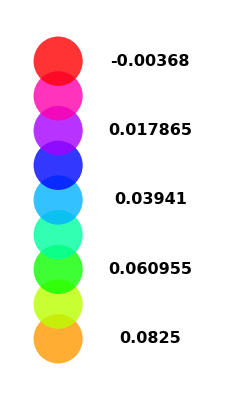

```mathematica
legd=Graphics[Array[{Hue[#1],Opacity[.8],Disk[{0,#1+10.},.08]}&,9,{0.1,1.}],Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Array[#1&,5,Reverse@{-0.0036800,0.082500}],Array[{.3,#1}&,5,{10.1,11.}]}]),Axes->False,PlotRange->{{-.12,.5},All}]
```

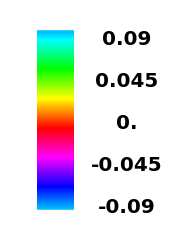

```mathematica
legdevo=Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{-0.46,0.54}],Axes->False,Epilog->(Inset[Style[#1,Bold,20],#2]&@@@Transpose[{Array[#1&,5,{-0.09,0.09}],Array[{.5,#1}&,5,{9.55,10.5}]}]),PlotRange->{{-.12,.72},{9.5,10.6}}]
```

```mathematica
bsize=20;
```

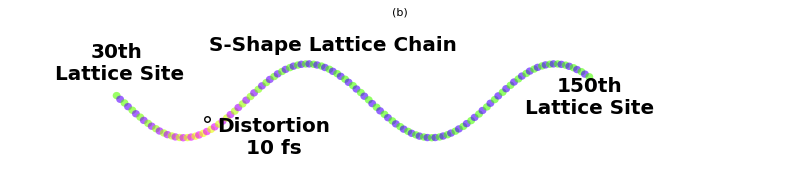

```mathematica
cf[1]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[1]]]}][[30;;150]],ImageSize->800,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[legdevo,{170,0},Automatic,24],Inset[Style["S-Shape Lattice Chain",Bold,bsize],{85.,15.}],Inset[Style["Distortion\n10 fs",Bold,bsize],{70.,-10.}],Inset[Graphics[{Circle[{0,0},1]}],{53.,-5.},Automatic,30]},Axes->False,PlotRange->{{19,185},{-20,20}},PlotLabel->Style["(b)",Bold,asize]]
```

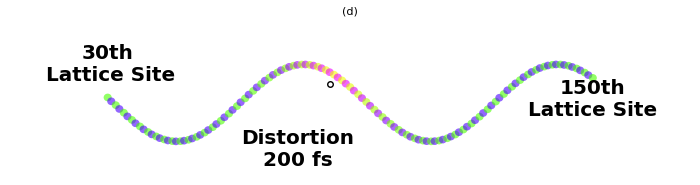

```mathematica
cf[2]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[20]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style[" ",Bold,bsize],{135.,-10.}],Inset[Style["Distortion\n200 fs",Bold,bsize],{77.,-12.}],Inset[Graphics[{Circle[{0,0},1]}],{85.,5.},Automatic,30]},Axes->False,PlotRange->{{20,160},{-17,20}},PlotLabel->Style["(d)",Bold,asize]]
```

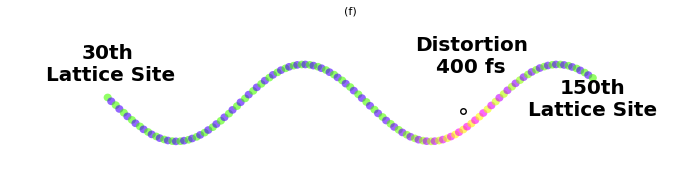

```mathematica
cf[3]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[40]]]}][[30;;150]],ImageSize->700,Epilog->{Inset[Style["30th\n Lattice Site",Bold,bsize],{30.,10.}],Inset[Style["150th\nLattice Site",Bold,bsize],{150.,1.}],Inset[Style[" ",Bold,bsize],{145.,-10.}],Inset[Style["Distortion\n400 fs",Bold,bsize],{120.,12.}],Inset[Graphics[{Circle[{0,0},1]}],{118.,-2},Automatic,30]},Axes->False,PlotRange->{{20,160},{-17,20}},PlotLabel->Style["(f)",Bold,asize]]
```

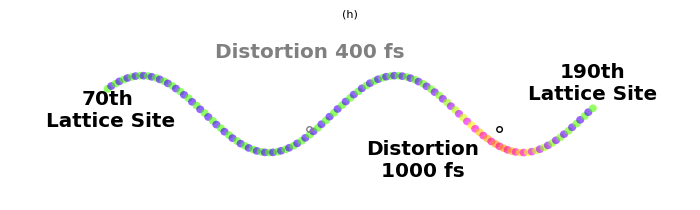

```mathematica
cf[4]=Graphics[{Hue[#2*5],Opacity[.6],Disk[{#1+#2,10*Sin[#1/10.]},1.]}&@@@Transpose[{Range[200],phiToU[config[[100]]]}][[70;;190]],ImageSize->700,Epilog->{Inset[Style["70th\n Lattice Site",Bold,bsize],{70.,1.}],Inset[Style["190th\nLattice Site",Bold,bsize],{190.,8.}],Inset[Style["Distortion 400 fs",Gray,Bold,bsize],{120.,16.}],Inset[Style[ " ",Bold,bsize],{115.,10.}],Inset[Style["Distortion\n1000 fs",Bold,bsize],{148.,-12.}],Inset[Graphics[{Dashed,Arrowheads[0.1],Gray,Thickness[0.01],Arrow[{{0,.8},{0,-.7}}]}],{120.,5.},Automatic,25],Inset[Graphics[{Circle[{0,0},1]}],{167.,-4.},Automatic,30],Inset[Graphics[{Dashed,Gray,Circle[{0,0},1]}],{120.,-4.},Automatic,30]},Axes->False,PlotRange->{{60,200},{-20,22}},PlotLabel->Style["(h)",Bold,asize]]
```

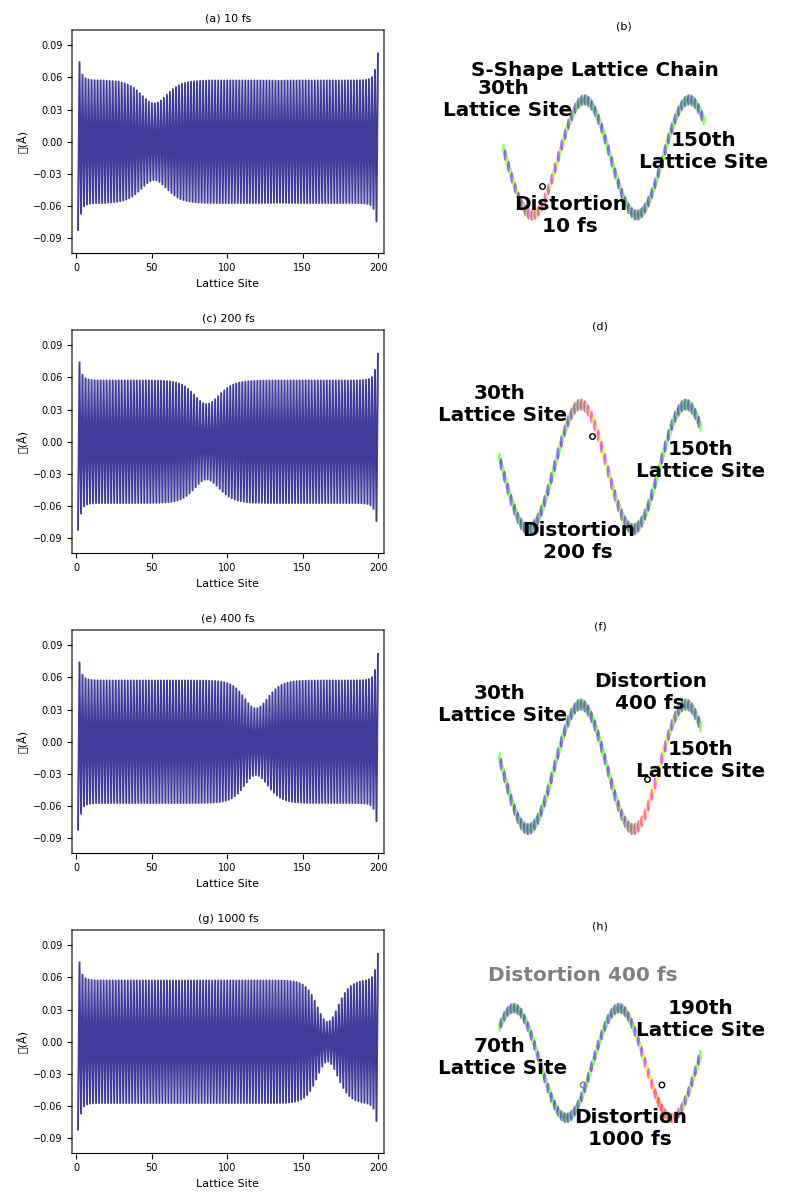

```mathematica
chf1=Grid[Transpose[{fa/@Range[4],cf/@Range[4]}]]
```

```mathematica
Export["chfigweakout.png",chf1,ImageResolution->300]
```

chfigweakout.png